```mathematica
ϵ=0.01;
zero=0;
(*corresponds to previewMask()*)
val2int[f_]:=zero+If[f[[1]]>ϵ,1,If[f[[1]]<-ϵ,2,If[Length[f]<2,0,If[f[[2]]>ϵ,3,If[f[[2]]<-ϵ,4,If[Length[f]<3,0,If[f[[3]]>ϵ,5,If[f[[3]]<-ϵ,6,0]]]]]]]];
minMax=zero+{0,6};
color=Blend[{Transparent,(*x>0*)Red,(*x<0*)Blue,(*y>0*)Green,(*y<0*)Purple,(*z>0*)Black,(*z<0*)Yellow},Rescale[#,minMax]]&;
```

```mathematica
NS=8;(*r3*)
SD=5;(*r2*)
DT=3;(*r1*)
CAP=10;
n=22;
n2=n/2;
```

```mathematica
ticks=Range[0,n-1];(*Join[ooo,n-1-ooo];*)
rng2={Min@ticks,Max@ticks};
ticks2=ticks-n2+0.5;
ticks2={ticks,ticks2}ᵀ;
ticks=ticks[[;;;;1]];
```

```mathematica
(*outwards oriented point boundary at iat*)
Rn[i_,il_,ir_]:=(i>=il&&i<ir);
Rn2[i_,il_,ir_]:=Rn[i,il,ir]||Rn[i,-ir,-il];

(*because zero is not at n2*dx but at (n2-0.5)*dx*)
PointB[i_,iat_]:=If[i==iat-1,Sign[i],0];
PointB2[i_,iat_]:=If[i==iat-1||i==-iat,Sign[i],0];
(*outwards oriented line boundary at jat from il to ir*)
SegmentB[i_,j_,jat_,il_,ir_]:=If[Rn[i,il,ir],PointB[j,jat],0];
SegmentBi2[i_,j_,jat_,il_,ir_]:=If[Rn2[i,il,ir],PointB[j,jat],0];
SegmentBj2[i_,j_,jat_,il_,ir_]:=If[Rn[i,il,ir],PointB2[j,jat],0];
SegmentBi2j2[i_,j_,jat_,il_,ir_]:=If[Rn2[i,il,ir],PointB2[j,jat],0];

(*outwards oriented plane boundary at kat from il to ir and jl to jr*)
PatchB[i_,j_,k_,kat_,il_,ir_,jl_,jr_]:=If[Rn[i,il,ir],SegmentB[j,k,kat,jl,jr],0];
PatchBi2[i_,j_,k_,kat_,il_,ir_,jl_,jr_]:=If[Rn2[i,il,ir],SegmentB[j,k,kat,jl,jr],0];
PatchBj2[i_,j_,k_,kat_,il_,ir_,jl_,jr_]:=If[Rn[i,il,ir],SegmentBi2[j,k,kat,jl,jr],0];
PatchBk2[i_,j_,k_,kat_,il_,ir_,jl_,jr_]:=If[Rn[i,il,ir],SegmentBj2[j,k,kat,jl,jr],0];
PatchBi2j2[i_,j_,k_,kat_,il_,ir_,jl_,jr_]:=If[Rn2[i,il,ir],SegmentBi2[j,k,kat,jl,jr],0];
PatchBi2k2[i_,j_,k_,kat_,il_,ir_,jl_,jr_]:=If[Rn2[i,il,ir],SegmentBj2[j,k,kat,jl,jr],0];
PatchBj2k2[i_,j_,k_,kat_,il_,ir_,jl_,jr_]:=If[Rn[i,il,ir],SegmentBi2j2[j,k,kat,jl,jr],0];
PatchBi2j2k2[i_,j_,k_,kat_,il_,ir_,jl_,jr_]:=If[Rn2[i,il,ir],SegmentBi2j2[j,k,kat,jl,jr],0];
```

## Regions 3D

```mathematica
N2S2e[i_,j_,k_]:={
PatchBi2j2k2[j,k,i,NS,0,SD,0,DT-1]+PatchBi2j2k2[k,j,i,NS,0,SD,0,DT-1],PatchBi2j2k2[k,i,j,NS,0,SD,0,DT-1]+PatchBi2j2k2[i,k,j,NS,0,SD,0,DT-1],PatchBi2j2k2[i,j,k,NS,0,SD,0,DT-1]+PatchBi2j2k2[j,i,k,NS,0,SD,0,DT-1]};
N2D2e[i_,j_,k_]:={
PatchBi2j2k2[j,k,i,SD,SD,NS,0,DT-1]+PatchBi2j2k2[k,j,i,SD,SD,NS,0,DT-1],PatchBi2j2k2[k,i,j,SD,SD,NS,0,DT-1]+PatchBi2j2k2[i,k,j,SD,SD,NS,0,DT-1],PatchBi2j2k2[i,j,k,SD,SD,NS,0,DT-1]+PatchBi2j2k2[j,i,k,SD,SD,NS,0,DT-1]};
N2T2e[i_,j_,k_]:={
PatchBi2j2k2[j,k,i,DT,DT-1,NS,DT-1,SD]+PatchBi2j2k2[k,j,i,DT,DT-1,NS,DT-1,SD],PatchBi2j2k2[k,i,j,DT,DT-1,NS,DT-1,SD]+PatchBi2j2k2[i,k,j,DT,DT-1,NS,DT-1,SD],
PatchBi2j2k2[i,j,k,DT,DT-1,NS,DT-1,SD]+PatchBi2j2k2[j,i,k,DT,DT-1,NS,DT-1,SD]};
S2D2e[i_,j_,k_]:=
{PatchBi2j2k2[j,k,i,SD,NS,CAP,0,DT]+PatchBi2j2k2[k,j,i,SD,NS,CAP,0,DT],
PatchBi2j2k2[k,i,j,SD,NS,CAP,0,DT]+PatchBi2j2k2[i,k,j,SD,NS,CAP,0,DT],
PatchBi2j2k2[i,j,k,SD,NS,CAP,0,DT]+PatchBi2j2k2[j,i,k,SD,NS,CAP,0,DT]};
S2T2e[i_,j_,k_]:={
PatchBi2j2k2[j,k,i,DT,NS,CAP,DT,SD]+PatchBi2j2k2[k,j,i,DT,NS,CAP,DT,SD],
PatchBi2j2k2[k,i,j,DT,NS,CAP,DT,SD]+PatchBi2j2k2[i,k,j,DT,NS,CAP,DT,SD],PatchBi2j2k2[i,j,k,DT,NS,CAP,DT,SD]+PatchBi2j2k2[j,i,k,DT,NS,CAP,DT,SD]};
D2T2e[i_,j_,k_]:={
PatchBi2j2k2[j,k,i,DT,SD,CAP,SD,CAP],
PatchBi2j2k2[k,i,j,DT,SD,CAP,SD,CAP],
PatchBi2j2k2[i,j,k,DT,SD,CAP,SD,CAP]};
S2CAP2e[i_,j_,k_]:={
PatchBi2j2k2[j,k,i,CAP,0,DT,0,SD]+PatchBi2j2k2[k,j,i,CAP,0,DT,0,SD],
PatchBi2j2k2[k,i,j,CAP,0,DT,0,SD]+PatchBi2j2k2[i,k,j,CAP,0,DT,0,SD],
PatchBi2j2k2[i,j,k,CAP,0,DT,0,SD]+PatchBi2j2k2[j,i,k,CAP,0,DT,0,SD]}
D2CAP2e[i_,j_,k_]:={
PatchBi2j2k2[j,k,i,CAP,SD,CAP,0,DT]+PatchBi2j2k2[k,j,i,CAP,SD,CAP,0,DT],
PatchBi2j2k2[k,i,j,CAP,SD,CAP,0,DT]+PatchBi2j2k2[i,k,j,CAP,SD,CAP,0,DT],
PatchBi2j2k2[i,j,k,CAP,SD,CAP,0,DT]+PatchBi2j2k2[j,i,k,CAP,SD,CAP,0,DT]}
T2CAP2e[i_,j_,k_]:={
PatchBi2j2k2[j,k,i,CAP,DT,CAP,DT,CAP](*+PatchBi2j2k2[k,j,i,CAP,DT,CAP,DT,CAP]*),
PatchBi2j2k2[k,i,j,CAP,DT,CAP,DT,CAP](*+PatchBi2j2k2[i,k,j,CAP,0,DT,CAP,DT,CAP]*),
PatchBi2j2k2[i,j,k,CAP,DT,CAP,DT,CAP](*+PatchBi2j2k2[j,i,k,CAP,0,DT,CAP,DT,CAP]*)}
```

```mathematica
(*plot b*)
Manipulate[
Graphics3D[Raster3D[Table[val2int@(If[n2s,N2S2e[i-n2,j-n2,k-n2],0]+If[n2d,N2D2e[i-n2,j-n2,k-n2],0]+If[n2t,N2T2e[i-n2,j-n2,k-n2],0]),{i,0,n-1},{j,0,n-1},{k,0,n-1}],ColorFunction->color],AxesLabel->{k,j,i},Ticks->{ticks,ticks,ticks},PlotRangePadding->0.5,ImageSize->Large,Axes->True],{n2s,{True,False}},{n2d,{True,False}},{n2t,{True,False}}]
```

```mathematica
(*plot c*)
Manipulate[
Graphics3D[Raster3D[Table[val2int@(If[s2d,S2D2e[i-n2,j-n2,k-n2],0]+If[s2t,S2T2e[i-n2,j-n2,k-n2],0]+If[d2t,D2T2e[i-n2,j-n2,k-n2],0]),{i,0,n-1},{j,0,n-1},{k,0,n-1}],ColorFunction->color],AxesLabel->{k,j,i},Ticks->{ticks,ticks,ticks},PlotRangePadding->0.5,ImageSize->Large,Axes->True],{s2d,{True,False}},{s2t,{True,False}},{d2t,{True,False}}]
```

```mathematica
(*all regions*)
Manipulate[
Graphics3D[Raster3D[Table[val2int@(If[n2s,N2S2e[i-n2,j-n2,k-n2],0]
+If[n2d,N2D2e[i-n2,j-n2,k-n2],0]
+If[n2t,N2T2e[i-n2,j-n2,k-n2],0]
+If[s2d,S2D2e[i-n2,j-n2,k-n2],0]
+If[s2t,S2T2e[i-n2,j-n2,k-n2],0]
+If[d2t,D2T2e[i-n2,j-n2,k-n2],0]
+If[s2cap,S2CAP2e[i-n2,j-n2,k-n2],0]
+If[d2cap,D2CAP2e[i-n2,j-n2,k-n2],0]
+If[t2cap,T2CAP2e[i-n2,j-n2,k-n2],0]),{i,0,n-1},{j,0,n-1},{k,0,n-1}],ColorFunction->color],AxesLabel->{k,j,i},Ticks->{ticks,ticks,ticks},PlotRangePadding->0.5,ImageSize->Large,Axes->True],{n2s,{True,False}},{n2d,{True,False}},{n2t,{True,False}},{s2d,{True,False}},{s2t,{True,False}},{d2t,{True,False}},{s2cap,{True,False}},{d2cap,{True,False}},{t2cap,{True,False}}]
```

## Regions 2D

```mathematica
N2Se[i_,j_]:={SegmentBi2j2[j,i,NS,0,SD],SegmentBi2j2[i,j,NS,0,SD]};
S2De[i_,j_]:={SegmentBi2j2[j,i,SD,NS,CAP],SegmentBi2j2[i,j,SD,NS,CAP]};

S2DeSYM[i_,j_]:={SegmentB[j,i,SD,NS,CAP]-SegmentB[-j-1,-i-1,SD,NS,CAP],SegmentB[i,j,SD,NS,CAP]-SegmentB[-i-1,-j-1,SD,NS,CAP]};
S2DeASYM[i_,j_]:={-SegmentB[j,-i-1,SD,NS,CAP]+SegmentB[-j-1,i,SD,NS,CAP],-SegmentB[i,-j-1,SD,NS,CAP]+SegmentB[-i-1,j,SD,NS,CAP]};

N2De[i_,j_]:={SegmentBi2j2[j,i,SD,SD,NS],SegmentBi2j2[i,j,SD,SD,NS]};

N2DeSYM[i_,j_]:={SegmentB[j,i,SD,SD,NS]-SegmentB[-j-1,-i-1,SD,SD,NS],SegmentB[i,j,SD,SD,NS]-SegmentB[-i-1,-j-1,SD,SD,NS]};
N2DeASYM[i_,j_]:={-SegmentB[j,-i-1,SD,SD,NS]+SegmentB[-j-1,i,SD,SD,NS],-SegmentB[i,-j-1,SD,SD,NS]+SegmentB[-i-1,j,SD,SD,NS]};

S2CAPe[i_,j_]:={SegmentBi2j2[j,i,CAP,0,SD],SegmentBi2j2[i,j,CAP,0,SD]};
D2CAPe[i_,j_]:={SegmentBi2j2[j,i,CAP,SD,CAP],SegmentBi2j2[i,j,CAP,SD,CAP]};
```

```mathematica
Manipulate[
MatrixPlot[Reverse@Table[val2int@(If[s2d,S2De[i-n2,j-n2],0]+If[n2s,N2Se[i-n2,j-n2],0]+If[n2d,N2De[i-n2,j-n2],0]+If[s2cap,S2CAPe[i-n2,j-n2],0]+If[d2cap,D2CAPe[i-n2,j-n2],0]),{i,0,n-1},{j,0,n-1}],ColorFunction->color,ColorFunctionScaling->False,FrameLabel->{{j,y},{x,i}},FrameTicks->{{ticks,ticks2},{ticks2,ticks}},DataRange->{rng2,rng2},DataReversed->True,GridLines->{{n2-0.5},{n2-0.5}},PlotRangePadding->0,ImageSize->Large],{{n2s,False},{True,False}},{{n2d,False},{True,False}},{{s2d,True},{True,False}},{{s2cap,False},{True,False}},{{d2cap,False},{True,False}}]
```

## ManhatanSphere

```mathematica
Cube3e[i_,j_,k_]:={
PatchBi2j2k2[j,k,i,CAP,0,CAP,0,CAP],
PatchBi2j2k2[k,i,j,CAP,0,CAP,0,CAP],
PatchBi2j2k2[i,j,k,CAP,0,CAP,0,CAP]}
Graphics3D[Raster3D[Table[val2int@Cube3e[i-n2,j-n2,k-n2],{i,0,n-1},{j,0,n-1},{k,0,n-1}],ColorFunction->color],AxesLabel->{k,j,i},Ticks->{ticks,ticks,ticks},PlotRangePadding->0.5,ImageSize->Large,Axes->True]
```

-Graphics3D-

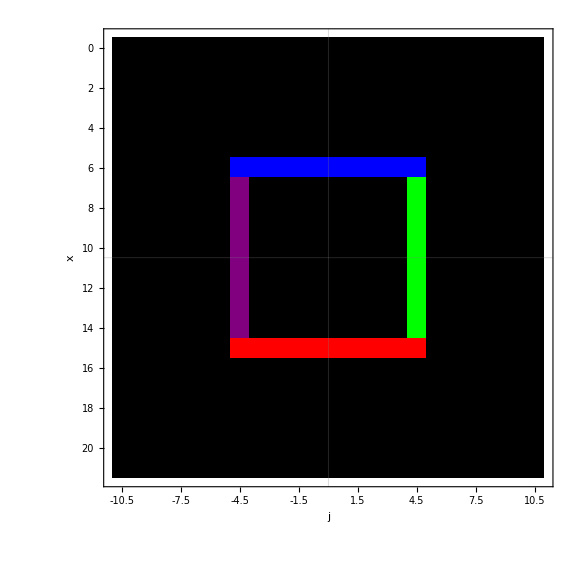

```mathematica
Cube2e[i_,j_]:={
SegmentBi2j2[j,i,CAP/2,0,CAP/2],
SegmentBi2j2[i,j,CAP/2,0,CAP/2]};
MatrixPlot[Reverse@Table[val2int@Cube2e[i-n2,j-n2],{i,0,n-1},{j,0,n-1}],ColorFunction->color,ColorFunctionScaling->False,FrameLabel->{{j,y},{x,i}},FrameTicks->{{ticks,ticks2},{ticks2,ticks}},DataRange->{rng2,rng2},DataReversed->True,GridLines->{{n2-0.5},{n2-0.5}},PlotRangePadding->0,ImageSize->Large]
```

## Regions 1D

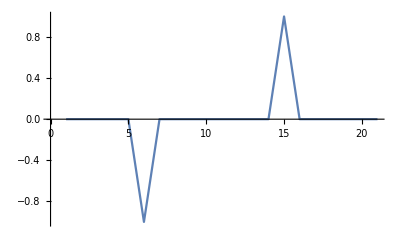

```mathematica
ListLinePlot[Table[PointB2[i-10,5],{i,0,20}]]
```

## Verification methods

∇·j+(∂ρ)/(∂t)=0

## Old Backup

```mathematica
S2D2e[i_,j_,k_]:=
{PatchBi2k2[j,k,i,SD,NS,CAP,-DT,DT]+PatchBj2k2[j,k,i,SD,-DT,DT,NS,CAP],PatchBi2k2[k,i,j,SD,NS,CAP,-DT,DT]+PatchBj2k2[k,i,j,SD,-DT,DT,NS,CAP],PatchBi2k2[i,j,k,SD,NS,CAP,-DT,DT]+PatchBj2k2[i,j,k,SD,-DT,DT,NS,CAP]};
Graphics3D[Raster3D[Table[val2int@S2D2e[i-n2,j-n2,k-n2],{i,0,n-1},{j,0,n-1},{k,0,n-1}],ColorFunction->color(*,ColorFunctionScaling->False*)],AxesLabel->{k,j,i},Ticks->{ticks,ticks,ticks},(*DataRange->{rng,rng,rng},*)PlotRangePadding->0.5,ImageSize->Large,(*BoxRatios->{1, 1, 1}*)Axes->True]
```

```mathematica
S2T2e[i_,j_,k_]:={
PatchBi2j2k2[j,k,i,DT,NS,CAP,DT,SD]+PatchBi2j2k2[j,k,i,DT,DT,SD,NS,CAP],
PatchBi2j2k2[k,i,j,DT,NS,CAP,DT,SD]+PatchBi2j2k2[k,i,j,DT,DT,SD,NS,CAP],PatchBi2j2k2[i,j,k,DT,NS,CAP,DT,SD]+PatchBi2j2k2[i,j,k,DT,DT,SD,NS,CAP]}
Graphics3D[Raster3D[Table[val2int@(S2T2e[i-n2,j-n2,k-n2]+S2D2e[i-n2,j-n2,k-n2]),{i,0,n-1},{j,0,n-1},{k,0,n-1}],ColorFunction->color(*,ColorFunctionScaling->False*)],AxesLabel->{k,j,i},Ticks->{ticks,ticks,ticks},(*DataRange->{rng,rng,rng},*)PlotRangePadding->0.5,ImageSize->Large,(*BoxRatios->{1, 1, 1}*)Axes->True]
```

```mathematica
D2T2e[i_,j_,k_]:={
PatchBi2j2k2[j,k,i,DT,SD,CAP,SD,CAP],
PatchBi2j2k2[k,i,j,DT,SD,CAP,SD,CAP],
PatchBi2j2k2[i,j,k,DT,SD,CAP,SD,CAP]}
Graphics3D[Raster3D[Table[val2int@(D2T2e[i-n2,j-n2,k-n2](*+S2D2e[i-n2,j-n2,k-n2]*)),{i,0,n-1},{j,0,n-1},{k,0,n-1}],ColorFunction->color(*,ColorFunctionScaling->False*)],AxesLabel->{k,j,i},Ticks->{ticks,ticks,ticks},(*DataRange->{rng,rng,rng},*)PlotRangePadding->0.5,ImageSize->Large,(*BoxRatios->{1, 1, 1}*)Axes->True]
```

```mathematica
N2T2e[i_,j_,k_]:={
PatchBi2j2k2[j,k,i,DT,DT,NS,DT,SD]+PatchBi2j2k2[k,j,i,DT,DT,NS,DT,SD],PatchBi2j2k2[k,i,j,DT,DT,NS,DT,SD]+PatchBi2j2k2[i,k,j,DT,DT,NS,DT,SD],
PatchBi2j2k2[i,j,k,DT,DT,NS,DT,SD]+PatchBi2j2k2[j,i,k,DT,DT,NS,DT,SD]}
Graphics3D[Raster3D[Table[val2int@(N2T2e[i-n2,j-n2,k-n2](*+D2T2e[i-n2,j-n2,k-n2]*)(*+S2D2e[i-n2,j-n2,k-n2]*)),{i,0,n-1},{j,0,n-1},{k,0,n-1}],ColorFunction->color(*,ColorFunctionScaling->False*)],AxesLabel->{k,j,i},Ticks->{ticks,ticks,ticks},(*DataRange->{rng,rng,rng},*)PlotRangePadding->0.5,ImageSize->Large,(*BoxRatios->{1, 1, 1}*)Axes->True]
```

```mathematica
N2D2e[i_,j_,k_]:={
PatchBi2j2k2[j,k,i,SD,SD,NS,0,DT]+PatchBi2j2k2[k,j,i,SD,SD,NS,0,DT],PatchBi2j2k2[k,i,j,SD,SD,NS,0,DT]+PatchBi2j2k2[i,k,j,SD,SD,NS,0,DT],PatchBi2j2k2[i,j,k,SD,SD,NS,0,DT]+PatchBi2j2k2[j,i,k,SD,SD,NS,0,DT]}
Graphics3D[Raster3D[Table[val2int@(N2D2e[i-n2,j-n2,k-n2](*+D2T2e[i-n2,j-n2,k-n2]*)(*+S2D2e[i-n2,j-n2,k-n2]*)),{i,0,n-1},{j,0,n-1},{k,0,n-1}],ColorFunction->color(*,ColorFunctionScaling->False*)],AxesLabel->{k,j,i},Ticks->{ticks,ticks,ticks},(*DataRange->{rng,rng,rng},*)PlotRangePadding->0.5,ImageSize->Large,(*BoxRatios->{1, 1, 1}*)Axes->True]
```

```mathematica
N2S2e[i_,j_,k_]:={
PatchBi2j2k2[j,k,i,NS,-SD,SD,-DT,DT]+PatchBi2j2k2[k,j,i,NS,-SD,SD,-DT,DT],PatchBi2j2k2[k,i,j,NS,-SD,SD,-DT,DT]+PatchBi2j2k2[i,k,j,NS,-SD,SD,-DT,DT],PatchBi2j2k2[i,j,k,NS,-SD,SD,-DT,DT]+PatchBi2j2k2[j,i,k,NS,-SD,SD,-DT,DT]}
Graphics3D[Raster3D[Table[val2int@(N2S2e[i-n2,j-n2,k-n2](*+D2T2e[i-n2,j-n2,k-n2]*)(*+S2D2e[i-n2,j-n2,k-n2]*)),{i,0,n-1},{j,0,n-1},{k,0,n-1}],ColorFunction->color(*,ColorFunctionScaling->False*)],AxesLabel->{k,j,i},Ticks->{ticks,ticks,ticks},(*DataRange->{rng,rng,rng},*)PlotRangePadding->0.5,ImageSize->Large,(*BoxRatios->{1, 1, 1}*)Axes->True]
```

## Stare implementacje

```mathematica
(*ret=0;*)
(*ret=If[((i==SD||i==n-1-SD)&&((j>CAP&&j<NS)||(j<n-1-CAP&&j>n-1-NS))),0+ⅈ Sign[i-n2],ret];ret=If[((j==SD||j==n-1-SD)&&((i>CAP&&i<NS)||(i<n-1-CAP&&i>n-1-NS))),Sign[j-n2]+ⅈ 0,ret];*)
(*ret={S2Dbox[j,i]+S2Dbox[i,j], 
S2Dbox[i,j]+S2Dbox[j,i], 
S2Dbox[j,k]+S2Dbox[k,j]};*)
```

```mathematica
(*S2D[i_,j_,k_]:=Block[{ret},
ret=0;

ret=If[(k<n-1-SD&& k>SD)&&((i==SD||i==n-1-SD)&&((j>CAP&&j<NS)||(j<n-1-CAP&&j>n-1-NS))),{0,Sign[i-n2]},ret];ret=If[(k<n-1-SD&& k>SD)&&((j==SD||j==n-1-SD)&&((i>CAP&&i<NS)||(i<n-1-CAP&&i>n-1-NS))),{Sign[j-n2],0},ret];

ret=If[(i<n-1-SD&& i>SD)&&((j==SD||j==n-1-SD)&&((k>CAP&&k<NS)||(k<n-1-CAP&&k>n-1-NS))),{0, Sign[j-n2]},ret];ret=If[(i<n-1-SD&& i>SD)&&((k==SD||k==n-1-SD)&&((j>CAP&&j<NS)||(j<n-1-CAP&&j>n-1-NS))),{Sign[k-n2],0},ret];

ret=If[(j<n-1-SD&& j>SD)&&((k==SD||k==n-1-SD)&&((i>CAP&&i<NS)||(i<n-1-CAP&&i>n-1-NS))),{0, Sign[k-n2]},ret];ret=If[(j<n-1-SD&& j>SD)&&((i==SD||i==n-1-SD)&&((k>CAP&&k<NS)||(k<n-1-CAP&&k>n-1-NS))),{Sign[i-n2], 0},ret];

ret];*)
```

```mathematica
(*ret=0;*)
(*ret=If[((i==SD||i==n-1-SD)&&((j>CAP&&j<NS)||(j<n-1-CAP&&j>n-1-NS))),0+ⅈ Sign[i-n2],ret];ret=If[((j==SD||j==n-1-SD)&&((i>CAP&&i<NS)||(i<n-1-CAP&&i>n-1-NS))),Sign[j-n2]+ⅈ 0,ret];*)
(*ret={S2Dbox[j,i]+S2Dbox[i,j], 
S2Dbox[i,j]+S2Dbox[j,i], 
S2Dbox[j,k]+S2Dbox[k,j]};*)
```